### Make a Table of ⅆ^n/(ⅆ x^n)( x^n Sin[n x]) for n=1,8 Use Simplify to simplify the results and use TableForm to make a nicely formatted table. The results should look like this:

```mathematica
f=x^n * Sin[n*x]
```

```mathematica
D[f,x]
```

n x^n Cos[n x]+n x^(-1+n) Sin[n x]

```mathematica
D[f,{x,2}]
```

2 n^2 x^(-1+n) Cos[n x]+(-1+n) n x^(-2+n) Sin[n x]-n^2 x^n Sin[n x]

```mathematica
TableForm[Table[{n,Simplify[D[f,{x,n}]]},{n,1,8}]]
```

1 | x Cos[x]+Sin[x]
2 | 8 x Cos[2 x]+2 (1-2 x^2) Sin[2 x]
3 | -27 x (-2+x^2) Cos[3 x]+3 (2-27 x^2) Sin[3 x]
4 | 8 (-16 x (-3+8 x^2) Cos[4 x]+(3-144 x^2+32 x^4) Sin[4 x])
5 | 5 (25 x (24-200 x^2+25 x^4) Cos[5 x]+(24-3000 x^2+3125 x^4) Sin[5 x])
6 | -144 (-36 x (5-100 x^2+54 x^4) Cos[6 x]+(-5+1350 x^2-4050 x^4+324 x^6) Sin[6 x])
7 | -7 (49 x (-720+29400 x^2-43218 x^4+2401 x^6) Cos[7 x]+(-720+370440 x^2-2521050 x^4+823543 x^6) Sin[7 x])
8 | 128 (-64 x (-315+23520 x^2-75264 x^4+16384 x^6) Cos[8 x]+(315-282240 x^2+3763200 x^4-3211264 x^6+131072 x^8) Sin[8 x])

### Use Series to find a simple approximation for 1/(√(a+ b x^2)) valid near x≈0. Make a plot that compares the the function and its series approximation. It should look something like

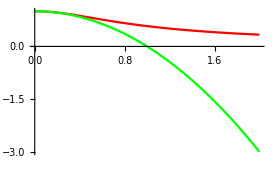

```mathematica
func=1/Sqrt[a+b*x^2]
```

1/(√(a+b x^2))

```mathematica
se1=Normal[Series[func,{x,0,10}]]
```

1/(√a)-(b x^2)/(2 a^(3/2))+(3 b^2 x^4)/(8 a^(5/2))-(5 b^3 x^6)/(16 a^(7/2))+(35 b^4 x^8)/(128 a^(9/2))-(63 b^5 x^10)/(256 a^(11/2))

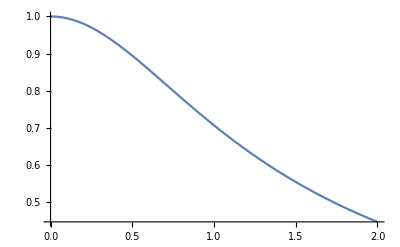

```mathematica
plot1=Plot[1/Sqrt[a+b*x^2]/. {a->1,b->1},{x,0,2}]
```

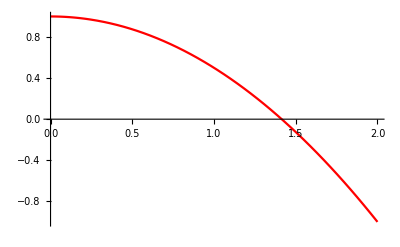

```mathematica
plot2=Plot[Evaluate[Normal[Series[func,{x,0,2}]]/. {a->1,b->1}],{x,0,2},PlotStyle-> Red]
```

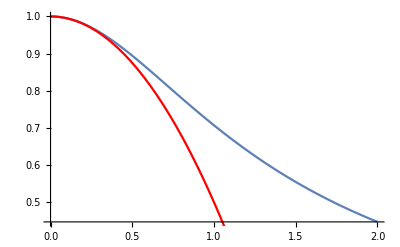

```mathematica
Show[plot1,plot2]
```